```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_surface"];
filesMesh={"retouched_position_energy_sp.out.m"};
meshData=Table[ReadList[filesMesh[[i]],{Number, Number,Number,Number, Number,Number}],{i,1,1}];
```

```mathematica
sliceData=Table[Partition[meshData[[1]],121][[i]],{i,1,11}];
contours=Table[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]],Transpose[sliceData[[i]]][[6]]},{i,1,11}];
```

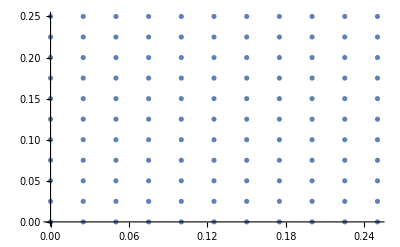

```mathematica
ListPlot@N[Transpose[{Transpose[sliceData[[1]]][[1]],Transpose[sliceData[[1]]][[2]]}],3]
```

```mathematica
Transpose[Transpose@{Transpose[sliceData[[1]]][[1]],Transpose[sliceData[[1]]][[2]]}];
```

```mathematica
ListPlot@r0[Transpose@{Transpose[sliceData[[1]]][[1]],Transpose[sliceData[[1]]][[2]]}]
```

-Graphics-

```mathematica
r0=RotationTransform[0,{0.25,0.25}];
r90=RotationTransform[Pi/2,{0.25,0.25}];
r180=RotationTransform[Pi,{0.25,0.25}];
r270=RotationTransform[3*Pi/2,{0.25,0.25}];
contours0=Table[Transpose@{Transpose[r0[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[1]],Transpose[r0[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[2]],Transpose[sliceData[[i]]][[6]]},{i,1,11}];
contours90=Table[Transpose@{Transpose[r90[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[1]],Transpose[r90[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[2]],Transpose[sliceData[[i]]][[6]]},{i,1,11}];
contours180=Table[Transpose@{Transpose[r180[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[1]],Transpose[r180[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[2]],Transpose[sliceData[[i]]][[6]]},{i,1,11}];
contours270=Table[Transpose@{Transpose[r270[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[1]],Transpose[r270[Transpose@{Transpose[sliceData[[i]]][[1]],Transpose[sliceData[[i]]][[2]]}]][[2]],Transpose[sliceData[[i]]][[6]]},{i,1,11}];
```

```mathematica
jointData=Table[Partition[Flatten@Join[{contours0[[i]],contours90[[i]],contours180[[i]],contours270[[i]]}],3],{i,1,11}];
```

```mathematica
zrc=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_surface/FS_frenkel/Visualisation_paper/poscar.46579.perf.84.eps"];
```

```mathematica
zrc200=Show[ImageCrop[zrc],ImageSize->200];
```

```mathematica
plotStyleRot={InterpolationOrder->2,ClippingStyle->White,Frame->True,MaxPlotPoints->50,Contours->10,PlotRange->{Automatic,Automatic,{0,20}},PlotTheme->"Minimal",Mesh->True};
plotsFull=Flatten@{zrc200,Table[ListContourPlot[jointData[[i]],Evaluate@plotStyleRot],{i,1,11}]};
```

```mathematica
frenkelenergysurface=GraphicsGrid[Partition[plotsFull,6],ImageSize->1000,Spacings->{10,10},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]]]
```

-Graphics-

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkelenergysurface.pdf",frenkelenergysurface]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkelenergysurface.pdf

```mathematica
GraphicsGrid[{}]
```

```mathematica
ListContourPlot[contours0[[1]],Evaluate@plotStyleRot];
ListContourPlot[contours90[[1]],Evaluate@plotStyleRot];
ListContourPlot[contours180[[1]],Evaluate@plotStyleRot];
ListContourPlot[contours270[[1]],Evaluate@plotStyleRot];
```

```mathematica
GraphicsGrid[{plots[[1;;3]],plots[[4;;7]],plots[[8;;11]]},ImageSize->Full];
```

```mathematica
ListContourPlot[data,Contours->3,MaxPlotPoints->30,InterpolationOrder->1]
```

```mathematica
ListContourPlot[Table[Sin[j^2+i],{i,0,Pi,0.02},{j,0,Pi,0.02}],PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"z-value",LabelStyle->{Italic,FontFamily->"Helvetica"}],Above]]
```

```mathematica
plotStyle={InterpolationOrder->4,ClippingStyle->White,Frame->True,MaxPlotPoints->20,Contours->11,PlotRange->{{0,0.25},{0,0.25},{0,50}}};
plotStyle2={InterpolationOrder->4,ClippingStyle->White,Frame->True,MaxPlotPoints->20,Contours->11,PlotRange->{{0,0.25},{0,0.25},{0,50},PlotLegends->BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Energy",LabelStyle->{Italic,FontFamily->"Helvetica"}]}};
```

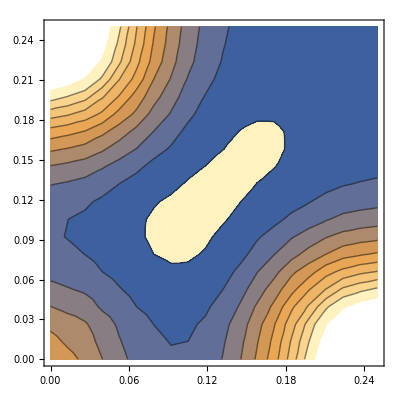

```mathematica
ListContourPlot[contours[[5]],plotStyle2]
```

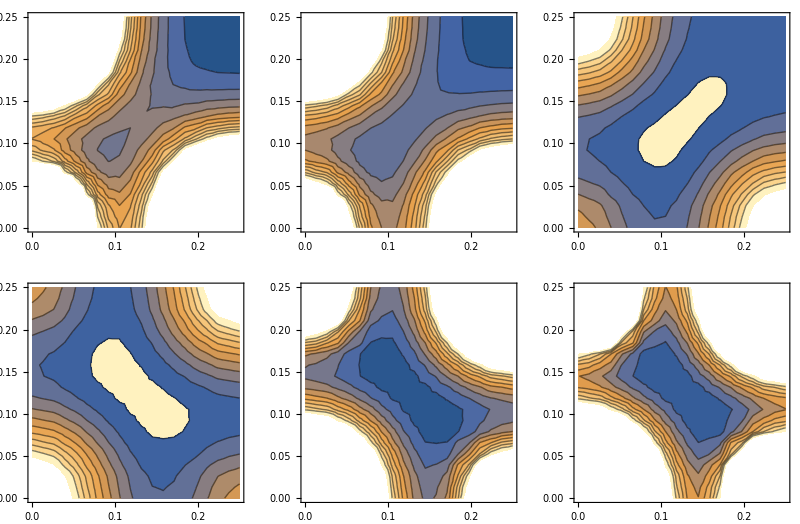

```mathematica
plots=Table[ListContourPlot[contours[[i]],plotStyle],{i,1,11}];
GraphicsGrid[{{plots[[1]],plots[[3]],plots[[5]]},{plots[[7]],plots[[9]],plots[[11]]}},ImageSize->800]
```

```mathematica
plots=Table[ListDensityPlot[contours[[i]],InterpolationOrder->4,ClippingStyle->Black,PlotTheme->"Minimal",MaxPlotPoints->20],{i,1,11}];
GraphicsGrid[{{plots[[1]],plots[[4]]},{plots[[8]],plots[[11]]}},ImageSize->Medium];
```